```mathematica
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
l=2;
m=1;
M=1`32;
a = .998`32M;
r0=10`32M;
Ω = 1/M 1/((r0/M)^(3/2)+a/M);
```

```mathematica
SpinWeightedSpheroidalHarmonicS[0,l,m,a m Ω,π/2,0]
```

SpinWeightedSpheroidalHarmonicS::prec: Spin-weighted spheroidal harmonic cannot be computed using "Leaver" method with the given working precision. To obtain an accurate result either provide a higher precision input spheroidicity or use the "SphericalExpansion" method instead.

0.

```mathematica
SpinWeightedSpheroidalHarmonicS[2,l,m,a m Ω,π/2,0]
```

-0.3132326444808793443872723117323

```mathematica
(*affects harmonics where they cross 0 at θ=π/2, see plots below*)
Table[{Print[l,m],SpinWeightedSpheroidalHarmonicS[0,l,m,a m Ω,π/2,0]},{l,1,5},{m,1,l}];
```

11

21

SpinWeightedSpheroidalHarmonicS::prec: Spin-weighted spheroidal harmonic cannot be computed using "Leaver" method with the given working precision. To obtain an accurate result either provide a higher precision input spheroidicity or use the "SphericalExpansion" method instead.

22

31

32

SpinWeightedSpheroidalHarmonicS::prec: Spin-weighted spheroidal harmonic cannot be computed using "Leaver" method with the given working precision. To obtain an accurate result either provide a higher precision input spheroidicity or use the "SphericalExpansion" method instead.

33

41

SpinWeightedSpheroidalHarmonicS::prec: Spin-weighted spheroidal harmonic cannot be computed using "Leaver" method with the given working precision. To obtain an accurate result either provide a higher precision input spheroidicity or use the "SphericalExpansion" method instead.

General::stop: Further output of SpinWeightedSpheroidalHarmonicS::prec will be suppressed during this calculation.

42

43

44

51

52

53

54

55

```mathematica
(*Compare this to plots form l∈[1,5]. Plots with zeroes at π/2 give the errors*)
```

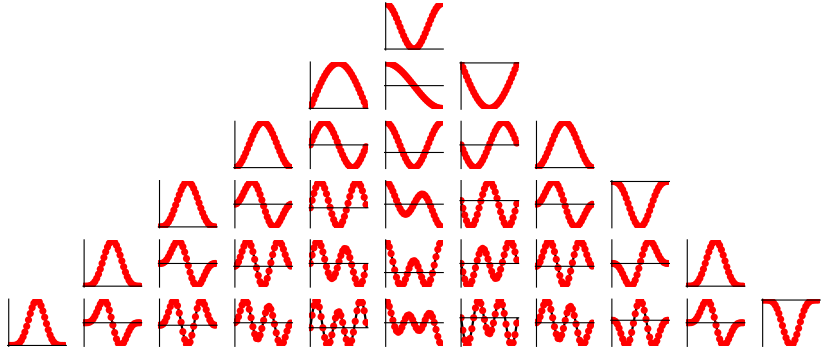

```mathematica
(*Checking if this happens with s=-2*)
```

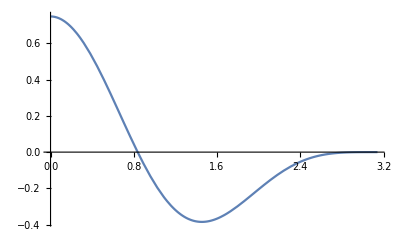

```mathematica
Plot[SpinWeightedSpheroidalHarmonicS[-2,3,2,a m Ω,θ,0],{θ,0,π}]
```

```mathematica
Θ=θ/.FindRoot[SpinWeightedSpheroidalHarmonicS[-2,3,2,a m Ω,θ,0],{θ,.82},AccuracyGoal->100,WorkingPrecision->100]
```

SpinWeightedSpheroidalHarmonicS::prec: Spin-weighted spheroidal harmonic cannot be computed using "Leaver" method with the given working precision. To obtain an accurate result either provide a higher precision input spheroidicity or use the "SphericalExpansion" method instead.

General::stop: Further output of SpinWeightedSpheroidalHarmonicS::prec will be suppressed during this calculation.

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

FindRoot::jsing: Encountered a singular Jacobian at the point {θ} = {0.8372682077573399686108833930089639008204021485824958330858691748514215259493620576091053752996450352}. Try perturbing the initial point(s).

0.8372682077573399686108833930089639008204021485824958330858691748514215259493620576091053752996450352

```mathematica
Precision[Θ]
SpinWeightedSpheroidalHarmonicS[-2,3,2,a m Ω,Θ,0]
```

100.

SpinWeightedSpheroidalHarmonicS::prec: Spin-weighted spheroidal harmonic cannot be computed using "Leaver" method with the given working precision. To obtain an accurate result either provide a higher precision input spheroidicity or use the "SphericalExpansion" method instead.

0.

```mathematica
(*The same error pops up near zeroes in this case as well. I suppose you're less likely to enter 0.837... as an argument than π/2, so the error won't appear often*)
```